```mathematica
ClearAll["Global`*"]
```

### Redoing the integrals, with the proper assumptions about d and Z_h along the way

```mathematica
integrand=(d+h^2)^(-(κ+1));
```

#### Integral 1: Z_h <0, d >0 (then integrate over z from 0 to Z_0'(1-b))

```mathematica
int1=Integrate[integrand,{h,zh,∞},Assumptions->{κ≥ 3/2,d>0,zh<0}]
```

1/2 d^-κ ((√π Gamma[1/2+κ])/(√d Gamma[1+κ])-(2 zh Hypergeometric2F1[1/2,1+κ,3/2,-zh^2/d])/d)

#### Integral 2: Z_h >0, d >0 (then integrate over z from Z_0'(1-b) to Z'_up)

```mathematica
int2=Integrate[integrand,{h,zh,∞},Assumptions->{κ≥ 3/2,d>0,zh>0}]
```

1/2 d^-κ ((√π Gamma[1/2+κ])/(√d Gamma[1+κ])-(2 zh Hypergeometric2F1[1/2,1+κ,3/2,-zh^2/d])/d)

#### Integral 3: Z_h >0, d <0 (then integrate over z from Z'_up to ∞)

```mathematica
int3=Integrate[integrand,{h,zh,∞},Assumptions->{κ>1.5,d<0,zh>0,Element[zh,Reals],Element[d,Reals],Element[κ,Reals]}]
```

Integrate[(d+h^2)^(-1-κ),{h,zh,∞},Assumptions→{κ>1.5,d<0,zh>0,zh∈ℝ,d∈ℝ,κ∈ℝ}]

```mathematica
FullSimplify[int3]
```

-1/(2 Gamma[1+κ])(1/d)^(1+κ) (ⅈ √-d √π Gamma[1/2+κ]+2 zh Gamma[1+κ] Hypergeometric2F1[1/2,1+κ,3/2,-zh^2/d])

No? How about this:

```mathematica
Integrate[(1+(1-b)h^2+b z0prime^2-b/(1-b)zprime^2)^(-(κ+1)),{h,zprime/(1-b)-z0prime,∞},Assumptions->{0≤ b<1,z0prime>0,κ≥1.5,Element[zprime,Reals],zprime≥0}]
```

ConditionalExpression[1/(1+2 κ)(1-b)^κ ((-1+b) z0prime+zprime)^(-1-2 κ) Hypergeometric2F1[1/2+κ,1+κ,3/2+κ,(-1+b^2 z0prime^2+b (1-z0prime^2+zprime^2))/((-1+b) z0prime+zprime)^2],b+(1. zprime)/z0prime≥1&&zprime>0&&((-1+b) z0prime+zprime)^2>0&&b (z0prime^2+zprime^2/(-1+b))>-1]

No? How about this:

```mathematica
Integrate[(1+c h^2+b z0prime^2-b/c zprime^2)^(-(κ+1)),{h,zprime/c-z0prime,∞},Assumptions->0≤ b≤ 1&&0≤ c≤1&&z0prime>0&&κ≥1.5&&Element[zprime,Reals]&&zprime≥0]
```

ConditionalExpression[1/(1+2 κ)c^κ (-c z0prime+zprime)^(-1-2 κ) Hypergeometric2F1[1/2+κ,1+κ,3/2+κ,-(c+b c z0prime^2-b zprime^2)/(-c z0prime+zprime)^2],zprime/c≥z0prime&&b zprime^2<c+b c z0prime^2&&zprime ((2 z0prime)/c+zprime)<1.+2. z0prime^2+zprime^2/c^2&&z0prime ((-1.-1. c) z0prime+2. zprime)<1.&&(-c z0prime+zprime)^2>0]

```mathematica
Integrate[g (1+(Z0prime-g)^2+b/(1-b)(g^2-z^2))^(-(κ+1)),{g,z,∞},Assumptions->Z0prime≥ 0&&z≥ 0&&b≤1&&b≥ 0&&κ≥ 1.5]
```

Integrate[g (1+(b (g^2-z^2))/(1-b)+(-g+Z0prime)^2)^(-1-κ),{g,z,∞},Assumptions→Z0prime≥0&&z≥0&&b≤1&&b≥0&&κ≥1.5]

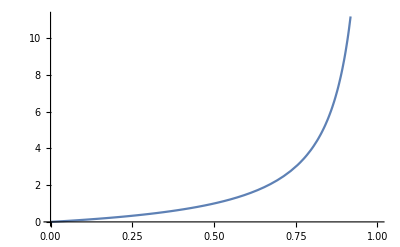

```mathematica
Plot[x/(1-x),{x,0,1}]
```

```mathematica
MaxwellIntegral1=Integrate[g Exp[-((1+b)/(1-b)g^2+b/(1-b)g vprime)],{g,vz-vprime,∞},Assumptions->0<b<1&&vprime>0]
```

1/4 (-(2 (-1+b) (-1+ⅇ^(((vprime-vz) (vprime-(1+b) vz))/(-1+b))))/(1+b)-(b ⅇ^((b^2 vprime^2)/(4-4 b^2)) √(π-b π) vprime Erf[(b vprime)/(2 √(1-b^2))])/(1+b)^(3/2)-((-1+b) (2 √(1-b^2)-b ⅇ^((b^2 vprime^2)/(4-4 b^2)) √π vprime+b ⅇ^((b^2 vprime^2)/(4-4 b^2)) √π vprime Erf[(b vprime)/(2 √(1-b^2))]))/((1+b) √(1-b^2))-(b ⅇ^((b^2 vprime^2)/(4-4 b^2)) vprime ((2+b) vprime-2 (1+b) vz) Erf[1/2 √(((2+b) vprime-2 (1+b) vz)^2/(1-b^2))])/((1+b)^(3/2) √(((2+b) vprime-2 (1+b) vz)^2/(π-b π))))

```mathematica
FullSimplify[MaxwellIntegral1]
```

1/4 (-(2 (-1+b) ⅇ^(((vprime-vz) (vprime-(1+b) vz))/(-1+b)))/(1+b)-(b ⅇ^((b^2 vprime^2)/(4-4 b^2)) √(π-b π) vprime)/(1+b)^(3/2)-(b ⅇ^((b^2 vprime^2)/(4-4 b^2)) √(π-b π) vprime √(-((2+b) vprime-2 (1+b) vz)^2/(-1+b^2)) Erf[((2+b) vprime-2 (1+b) vz)/(2 √(1-b^2))])/((1+b) √(-((2+b) vprime-2 (1+b) vz)^2/(-1+b))))